```mathematica
A=197; (*Au*)
Subscript[r, 0]=(1.12 A^(1/3)-0.86 A^(-1/3));(*fm*)
a=0.54 ;(*fm*)
Subscript[ρ, 0]=0.17;(*fm^-3*);
Subscript[σ, inel]=3;
ws[s_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s^2+z^2)-Subscript[r, 0])/a]));
```

```mathematica
ws2[s1_,s2_,ang1_,ang2_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang1-ang2]+z^2)-Subscript[r, 0])/a]));
ws1[s1_,s2_,ang_,z_]:=Subscript[ρ, 0]/(A(1+Exp[(√(s1^2+s2^2-2s1 s2 Cos[ang]+z^2)-Subscript[r, 0])/a]));
```

```mathematica
NIntegrate[2π s ws[s,z],{s,0,∞},{z,-∞,∞}]
```

1.00017

```mathematica
T[s_]:=NIntegrate[ws[s,z],{z,-∞,∞}]
```

```mathematica
T1[s1_,s2_,ang_]:=NIntegrate[ws1[s1,s2,ang,z],{z,-∞,∞}]
```

```mathematica
T2[s1_,s2_,ang1_,ang2_]:=NIntegrate[ws2[s1,s2,ang1,ang2,z],{z,-∞,∞}]
```

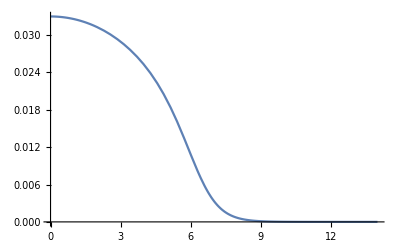

```mathematica
Plot[Subscript[σ, inel] T[x],{x,0,14}]
```

```mathematica
Quiet[NIntegrate[2π x T[x],{x,0,∞}]]
```

1.00016

```mathematica
Npart[b_]:=2 A Quiet[NIntegrate[2π T[s-b]s(1-(1-Subscript[σ, inel] T[s])^A),{s,0,∞}]]
```

```mathematica
Npart[0]
```

370.449

```mathematica
Npart[1]
```

474.981

```mathematica
Npart2[b_,ang_]:=2 A Quiet[NIntegrate[s T2[s,b,ang1,ang](1-(1-Subscript[σ, inel] T[s])^A),{s,0,∞},{ang1,0,2 π}]]
```

```mathematica
Npart2[0,0]
```

370.449

```mathematica
Npart2[0,π]
```

370.449

```mathematica
Npart2[1,0]
```

363.798

```mathematica
Npart2[1,π]
```

363.798

```mathematica
Npart1[b_]:=2 A Quiet[NIntegrate[s T1[s,b,ang](1-(1-Subscript[σ, inel] T[s])^A),{s,0,∞},{ang,0,2 π}]]
```

```mathematica
Npart1[0]
```

370.449

```mathematica
Npart1[1]
```

363.798

```mathematica
NpartTab=Table[{b,Npart1[b]},{b,0,14,1}]
```

{{0,370.449},{1,363.798},{2,344.757},{3,315.907},{4,280.487},{5,241.374},{6,200.861},{7,160.811},{8,122.809},{9,88.2631},{10,58.4586},{11,34.5495},{12,17.413},{13,7.13826},{14,2.34182}}

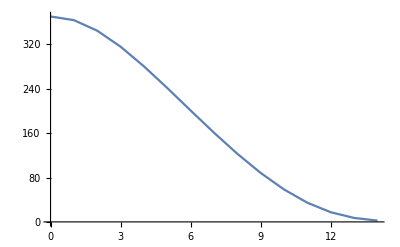

```mathematica
ListPlot[NpartTab,Joined->True]
```